```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
G = 4.302*10^(-3);
```

```mathematica
d= 9.36;
```

```mathematica
s =10^6 d Pi/(60*180);
```

```mathematica
1.34*^3/s
```

0.492156

```mathematica
datas= {{.25 s,55},{.5 s,92},{.75 s,110},{1 s,123},{1.25 s,134},{1.5 s,142},{1.75 s,145},{2 s,147},{2.25 s,148},{2.5 s,152},{2.75 s,155},{3 s,156},{3.5 s,157},{4 s,153},{4.5 s,153},{5 s,154},{5.5 s,153},{6 s,150},{6.5 s,149},{7 s,148},{7.5 s,146},{8 s,147},{8.5 s,148},{9 s,148},{9.5 s,149},{10 s,150},{10.5 s,150},{11 s,149}};
```

```mathematica
data= {{.25 ,55},{.5 ,92},{.75 ,110},{1 ,123},{1.25 ,134},{1.5 ,142},{1.75 ,145},{2 ,147},{2.25 ,148},{2.5 ,152},{2.75 ,155},{3 ,156},{3.5 ,157},{4 ,153},{4.5 ,153},{5 ,154},{5.5 ,153},{6 ,150},{6.5 ,149},{7 ,148},{7.5 ,146},{8 ,147},{8.5 ,148},{9 ,148},{9.5 ,149},{10 ,150},{10.5 ,150},{11 ,149}};
```

```mathematica
error = {8,8,6,5,4,4,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3};
```

```mathematica
dataerror = Table[Append[{data[[i]]},ErrorBar[error[[i]]]],{i,1,Length[data]}];
```

```mathematica
dataerrors=Table[Append[{datas[[i]]},ErrorBar[error[[i]]]],{i,1,Length[data]}];
```

```mathematica
disk[c_,r0_,r_]:= Sqrt[ 1/2c*G /(r0^3) r^2(BesselI[0,r /(2 r0)]BesselK[0,r /(2 r0)]-BesselI[1,r /(2 r0)]BesselK[1,r /(2 r0)])];
```

```mathematica
halo[c_,r0_,r_]:= Sqrt[ c*4*Pi*G*(r-r0 ArcTan[r/r0])/r];
```

```mathematica
diskhalo[cd_,ch_,rd_,rh_,r_]:= Sqrt[disk[cd,rd,r]^2+halo[ch,rh,r]^2];
```

```mathematica
fitdisk =NonlinearModelFit[datas,{disk[n,s,r]},{n},r,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
fitdisk["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
n | 5.91911×10^10 | 3.61292×10^8 | 163.832 | 5.14285×10^-42

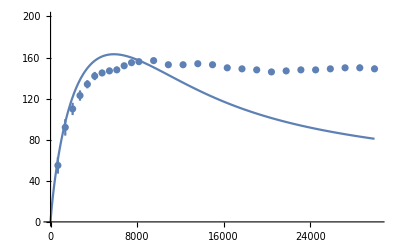

```mathematica
Show[Plot[disk[4.356*^10,s,r],{r,0,11s},PlotRange->{{0,11.1s},{0,200}}],ErrorListPlot[dataerrors]]
```

```mathematica
4.84*9
```

43.56

```mathematica
fitdiskhalo=NonlinearModelFit[datas,{diskhalo[cd,ch,s,rd,r],{rd>0&&cd>0&&ch>0}},{rd,{cd,4.31982*10^10},ch},r,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
fitdiskhalo["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
rd | 21606.9 | 2535.2 | 8.52275 | 7.26985×10^-9
cd | 4.31631×10^10 | 5.96366×10^8 | 72.377 | 1.43874×10^-30
ch | 1.01776×10^6 | 145341. | 7.00255 | 2.43474×10^-7

```mathematica
13.2/9
```

1.46667

```mathematica
13.966/9
```

1.55178

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {rd, 1.3437683365745332, 0.18995409144774272, 7.074174219322937, 2.0497286301719545*^-7}, {cd, 1.3198198726866132*^7, 1.4985940558020866*^6, 8.80705396886291, 3.8998596105362884*^-9}, {ch, 393118.4452694335, 5983.671870739516, 65.69852989295825, 1.5988062339194322*^-29}}
```

```mathematica
Show[Plot[diskhalo[1.3198198726866132*^10,391734,s,1.3437683365745332*^3,r],{r,0,11*s},PlotRange->{{0,11.1*s},{0,200}},PlotStyle->{Orange},PlotLabel->"NGC3198 Disk and Halo",AxesLabel->{"r [kpc]","v [km s^-1]"}],ErrorListPlot[dataerrors,PlotMarkers->{Automatic,4}]]
```

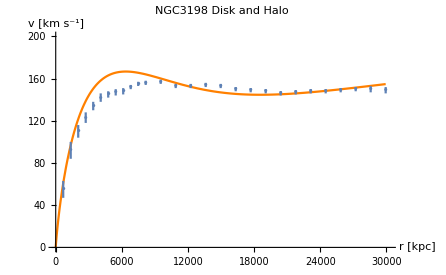

```mathematica
Show[Plot[fitdiskhalo[r],{r,0,11*s},PlotRange->{{0,11.1*s},{0,200}},PlotStyle->{Orange},PlotLabel->"NGC3198 Disk and Halo",AxesLabel->{"r [kpc]","v [km s^-1]"}],ErrorListPlot[dataerrors,PlotMarkers->{Automatic,4}]]
```

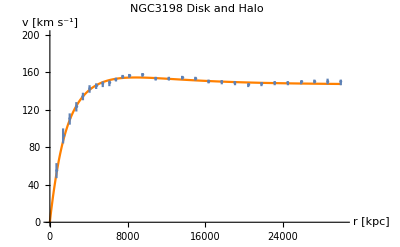

```mathematica
11*10^(-3) s
```

0.0299498

```mathematica
Assuming[r0>0,Limit[ArcTan[r]/r,r->∞]]
```

```mathematica
Assuming[r0>0,Integrate[r^4/(r^2+r0^2),{r,0,11r0}]]
```

1/3 r0^3 (1298+3 ArcTan[11])

```mathematica
N[ArcTan[11]]
```

```mathematica
s
```

```mathematica
G = 4.302*10^(-3);
```

```mathematica
c = 1.7174697366215695*^7;(* 17.17484229503409 *)
```

```mathematica
cd = 6.015105133051712*^6;
```

```mathematica
ch=21375;
```

```mathematica
Sig0 = c*10^(-6)/(Pi G);
```

```mathematica
Sig1 = cd/(Pi G);
```

```mathematica
sig = ch/(4Pi G);
```

```mathematica
Sig0
```

```mathematica
M0 = 2*Pi*Sig0*(10^6*s)^2;
```

```mathematica
M1 = 2*Pi*Sig1*s^2;
```

```mathematica
M0
```

5.91906×10^10

```mathematica
m=4.78*(9*10^9);
```

```mathematica
m/(2 Pi (2720)^2)
```

```mathematica
%*Pi*G
```

```mathematica
G
```

```mathematica
s
```

```mathematica
Quit
```

```mathematica
17.17484229503409
```

```mathematica
%/(9*10^9)
```

6.57673

```mathematica
%/(9*10^9)
```

6.57679

```mathematica
Integrate[r Exp[-a r],{r,0,11/a}]
```

(1-12/ⅇ^11)/a^2

```mathematica
N[1-12/ⅇ^11]
```

0.9998

```mathematica
NumberForm[0.999799579590517,16]
```

```mathematica
"0.999799579590517"*100
```

```mathematica
99.9799579590517*
```

```mathematica
9
```

```mathematica
0.999799579590517*1.32*10^10
```

1.31974×10^10

```mathematica
a = 1/s;
```

```mathematica
r0 = 1.34*^3;
```

```mathematica
sig0 = 3.93*^5;
```

```mathematica
N[ 4Pi sig0(11/a-r0 ArcTan[11/(a r0)])]
```

1.37811×10^11